```mathematica
ClearAll[tex,tf,mf,df,primeQpos,tr,u,id, bnTab];
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQpos[n_]:=If[PrimeQ[n]&&n>0,True,False]
tr:=Trace
u[m_Integer]:=1
id[m_Integer]:=Floor[1/m]
bnTab[j_]:=Table[Binomial[n,k],{n,0,j},{k,0,n}]
```

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes ANT

Numerical Methods and Tools

## Bernoulli Polynomials

### Definition / Theorem

#### Example

```mathematica
Manipulate[
Column[{Plot[BernoulliB[k,x],{x,0,1}],BernoulliB[k,x],BernoulliB[k]}],{k,1,6,1}]
```

## Euler-MacLaurin Summation

### Definition / Theorem

#### Example: First Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k)
Sum[f[k],{k,1,100}]//N
```

18.5896

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])//Expand//Simplify
g[100]//N
```

(3+4 n-3 √(1+n))/(2 √(1+n))

18.55

#### Example: Second Order

```mathematica
ClearAll[f]
```

```mathematica
f[k_]:=k^4+2k
f[k_]:=1/(√k+k^2)
Sum[f[k],{k,1,4}]//N
```

0.833433

```mathematica
Integrate[f[x],{x,1,5}]-1/2(f[5]-f[1])+1/12(f'[5]-f'[1])//N;
g[n_]=Integrate[f[x],{x,1,n+1},Assumptions->{n>0}]-1/2(f[n+1]-f[1])+1/12(f'[n+1]-f'[1])//Expand//Simplify
g[4]//N//Chop
```

1/288 (87-48/((√(1+n)+(1+n)^2)^2)-(48 n)/((√(1+n)+(1+n)^2)^2)-12/(√(1+n) (√(1+n)+(1+n)^2)^2)-144/(√(1+n)+(1+n)^2)+64 √3 π-64 Log[8]+192 Log[1+1/(√(1+n))]-192 (-1)^(1/3) Log[1-(-1)^(1/3)/(√(1+n))]+192 (-1)^(2/3) Log[1+(-1)^(2/3)/(√(1+n))])

0.836458

## Abel Summation

### Definition

∑_(y<n⩽x) a(n) f(n) = A(x) f(x)-A(y)f(y)-∫_y^x A(t)f'(t)ⅆt

#### Example

Arithmetic Functions

## Harmonic Numbers

```mathematica
ClearAll[r,s,t,t1,t2,t3,t4]
r[n_]:=Binomial[(n+1)!+n,n]
s[n_]:=(r[n]-1)/((n+1)!)
t[n_]:=s[n]-(n+1)Floor[s[n]/(n+1)]
t1[n_]:=Mod[s[n],n+1]
t2[n_]:=Expand[Pochhammer[x+1,n]][[2]]/(x n!)
t3[n_]:=-StirlingS1[n+1,2]/StirlingS1[n+1,1]
t4[n_]:=Mod[Pochhammer[(n+1)!,n+1]/(n! ((n+1)!)^2)-1/((n+1)!),n+1]
```

```mathematica
1764/720
HarmonicNumber[6]
t[6]
t1[6]
t2[6]
t3[6]
t4[6]
```

49/20

49/20

49/20

«4 more identical outputs»

```mathematica
25 26 27
Pochhammer[25,3]
```

17550

17550

```mathematica
t4[n_]:=Mod[Pochhammer[(n+1)!,n+1]/(n! ((n+1)!)^2)-1/((n+1)!),n+1]
1+1/4+1/9
Expand[(x+1)(x+4)]
Expand[(x+2)(x+3)]
Expand[(x+1)(x+2)(x+3)(x+4)]
(24+50 x+35 x^2+10 x^3+x^4)/(6+5x+x^2)//Simplify
((x+1)(x+2)(x+3)(x+4)(x+1)(x+4))/((x+1)(x+2)(x+3)(x+4))//Simplify//Expand
```

49/36

4+5 x+x^2

6+5 x+x^2

24+50 x+35 x^2+10 x^3+x^4

4+5 x+x^2

4+5 x+x^2

```mathematica
Expand[(x+1)(x/2+1)(x/3+1)(x/4+1)(x/5+1)(x/6+1)]
```

1+(49 x)/20+(203 x^2)/90+(49 x^3)/48+(35 x^4)/144+(7 x^5)/240+x^6/720

```mathematica
HarmonicNumber[4,2]
(7/6)^2
```

205/144

49/36

```mathematica
tt1[n_]:=ⅇ^EulerGamma n Log[Log[n]]
tt1[10^8000]//N
```

## Highest power of prime p in n!

```mathematica
ClearAll[f]
f[n_,p_]:=Sum[Floor[n/p^i],{i,1,Ceiling[N[Log[n]]/Log[p]]}]/;p≤n
```

```mathematica
f[10,2]
f[10,3]
f[10,5]
f[10,7]
```

8

4

2

1

```mathematica
10!
```

3628800

```mathematica
2^8 3^4 5^2 7
```

3628800

## Moebius Function

### Definition

The Moebius function is defined as follows:
if n > 1 write n as n = ∏_(i=1)^k (p^α_i)_i and
	μ(1) = 1;
	μ(n) = (-1)^k if α_i=1 for all i
	μ(n) = 0 otherwise.

#### Example

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,Divisors[12]}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
6 | 1
12 | 0

```mathematica
TableForm[Table[{k,MoebiusMu[k]},{k,1,12}],TableHeadings->{None,{"k","μ[k]"}},TableAlignments->{Right}]
```

k | μ[k]
1 | 1
2 | -1
3 | -1
4 | 0
5 | -1
6 | 1
7 | -1
8 | 0
9 | 0
10 | 1
11 | -1
12 | 0

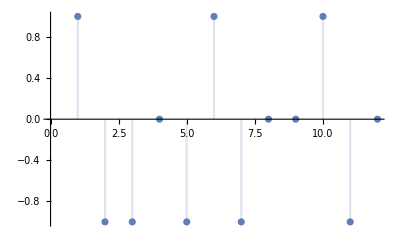

```mathematica
DiscretePlot[MoebiusMu[k],{k,12},AxesOrigin->{0,0}]
```

## Euler totient Function

### Definition

If n ≳ 1 the Euler totient ϕ(n) is defined to be the number of positive integers not exceeding n which are relatively prime to n.

Sum formula: n = ∑_(d/n) ϕ(d)

	n = ∑_(d/n) ϕ(d)
	ϕ(n) = ∑_(d/n) μ(n/d)d

Product formula: write n as n = ∏_(i=1)^k (p^α_i)_i and
	ϕ(n) = n∏_(i=1)^k (1-1/p_i)

#### Example

```mathematica
TableForm[Table[{k,EulerPhi[k]},{k,1,20}],TableHeadings->{None,{"k","ϕ[k]"}},TableAlignments->{Right}]
```

k | ϕ[k]
1 | 1
2 | 1
3 | 2
4 | 2
5 | 4
6 | 2
7 | 6
8 | 4
9 | 6
10 | 4
11 | 10
12 | 4
13 | 12
14 | 6
15 | 8
16 | 8
17 | 16
18 | 6
19 | 18
20 | 8

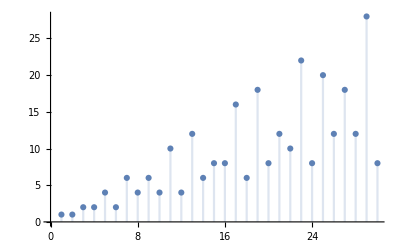

```mathematica
DiscretePlot[EulerPhi[k],{k,30},AxesOrigin->{0,0}]
```

```mathematica
Total[Map[EulerPhi[#]&,Divisors[100]]]
```

100

```mathematica
Divisors[100]
EulerPhi[100]
Total[Map[MoebiusMu[100/#]#&,Divisors[100]]]
```

{1,2,4,5,10,20,25,50,100}

40

40

## Dirichlet Multiplication ( Convolution )

### Definition

The Dirichlet convolution (f *g)(m) of two functions f(n) and g(n) is given by ∑_(d∣m) f(d) g(m/d).

#### Example

```mathematica
DirichletConvolve[MoebiusMu[n],id[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],u[n],n,12]
```

0

```mathematica
DirichletConvolve[MoebiusMu[n],n,n,12]
```

4

```mathematica
DirichletConvolve[MoebiusMu[n]^2 EulerPhi[n]^-1,u[n],n,12]
```

3

```mathematica
Table[{k,Log[2,DirichletConvolve[MoebiusMu[n]^2,u[n],n,k]],Total[Map[MoebiusMu[#]^2&,Divisors[k]]],2^PrimeNu[k]},{k,1,10}]//tf
```

1 | 0 | 1 | 1
2 | 1 | 2 | 2
3 | 1 | 2 | 2
4 | 1 | 2 | 2
5 | 1 | 2 | 2
6 | 2 | 4 | 4
7 | 1 | 2 | 2
8 | 1 | 2 | 2
9 | 1 | 2 | 2
10 | 2 | 4 | 4

```mathematica
DirichletConvolve[MoebiusMu[n],Log[n],n,729]//Simplify
```

Log[3]

Distribution of Prime Numbers

## Suppose π(n)=A ; for which m is π(m)=2A

```mathematica
Reduce[x/Log[x]==(2 y)/Log[y],x,Integers]
```

(x|y)∈ℤ&&((ProductLog[-Log[y]/(2 y)]≠0&&y≥2&&x==ⅇ^(-ProductLog[-Log[y]/(2 y)]))||(ProductLog[-1,-Log[y]/(2 y)]≠0&&y≥2&&x==ⅇ^(-ProductLog[-1,-Log[y]/(2 y)])))

```mathematica
ClearAll[f,g]
f[y_]:=ⅇ^(-ProductLog[-1,-Log[y]/(2 y)])
g[x_]:=x/Log[x]
```

```mathematica
f[100.]
2g[100.]
g[237.]
```

237.581

43.4294

43.3426

```mathematica
f[100000.]
2g[100000.]
g[213147.]
```

213147.

17371.8

17371.8

```mathematica
Table[f[10.^k]/10^k,{k,2,100000,10000}]//tf
```

2.37581
2.00006019657403
2.00003010064302
2.00002006761887
2.00001505091045
2.00001204082283
2.000010034071
2.00000860066431
2.0000075256022
2.00000668943902

## Sieve of Erasthostenes

```mathematica
ClearAll[f]
f[n_]:=ArrayPlot[Partition[Table[PrimeQ[k]/.{False->0,True->1},{k,n+1,n+10000}],100]]
```

```mathematica
f[1000000]
```

-Graphics-

```mathematica
Table[PrimePi[10^k],{k,1,9}]
```

{4,25,168,1229,9592,78498,664579,5761455,50847534}

## ChebyshevPsi and ChebyshevTheta

### Definition Psi, Theta

ψ(x) = ∑_n Λ(n)
θ(x) = ∑_p Log(p)

```mathematica
chebyshevPsi[x_]:=Sum[MangoldtLambda[y],{y,x}]
chebyshevTheta[x_]:=Sum[Log[k],{k,Select[Range[x],PrimeQ]}]
chebyshevPsi1[x_]:=Sum[chebyshevTheta[x^(1/m)],{m,1,Log[2,x]}]
```

#### Example

```mathematica
chebyshevPsi[10]
chebyshevTheta[10]+chebyshevTheta[3]+chebyshevTheta[2]
```

3 Log[2]+2 Log[3]+Log[5]+Log[7]

3 Log[2]+2 Log[3]+Log[5]+Log[7]

```mathematica
Table[{x,chebyshevPsi[x],chebyshevPsi1[x]},{x,10}]//tf
```

### Theorem:

0 ⩽(ψ(x))/x-(ϑ(x))/x⩽(Log(x))^2/(2 √x Log(2))

#### Example

```mathematica
Table[{x,chebyshevPsi[x]/x-chebyshevTheta[x]/x//N,Log[x]^2/(2 √x Log[2.])},{x,500000,1500000,500000}]//tf
```

500000 | 0.00159035 | 0.175664
1000000 | 0.00110242 | 0.137682
1500000 | 0.000902378 | 0.119113

#### Proof:

```mathematica
ClearAll[t1,t2,T1,T2];
t1[x_]:=chebyshevPsi[x]-chebyshevTheta[x]
t2[x_]:=Sum[chebyshevTheta[x^(1/m)],{m,2,Log[2,x]}]
T1[x_]:=Log[2,x] √x Log[√x]
T2[x_]:=Log[x]^2/(2 √x Log[2.])
```

```mathematica
t2[1000]//N
T1[1000]/1000//N
T2[1000]//N
```

40.4356

1.08847

1.08847

```mathematica
chebyshevTheta[100000]//N
100000Log[100000.]
```

99685.4

1.15129×10^6

### Theorem:

θ(x) =π(x) Log(x)-∫_2^x (π(t))/t ⅆt

#### Proof:

Let a(n) be the characteristic function of the primes.
Then ∑_(1<n≤x) a(n)=π(x) , i.e. the prime-counting function.
Then θ(x) = ∑_(p≤x) Log(p) = ∑_(1<n≤x) a(n)Log(n) .
Finally, by applying Abel Summation:
θ(x) =π(x) Log(x)-∫_2^x (π(t))/t ⅆt.

tmp’s

## tmp-1: Alternate Prime Definitions; No more Unique Prime Factorization

```mathematica
Divisors[46 51]
```

{1,2,3,6,17,23,34,46,51,69,102,138,391,782,1173,2346}

```mathematica
Divisors[391]
```

{1,17,23,391}

```mathematica
46 51
```

2346

```mathematica
6 391
```

2346

```mathematica
Divisors[391]
```

{1,17,23,391}

```mathematica
Divisors[21 46]
```

{1,2,3,6,7,14,21,23,42,46,69,138,161,322,483,966}

```mathematica
6 161
```

966

```mathematica
Divisors[161]
```

{1,7,23,161}

```mathematica
ClearAll[g]
g[x_]:=10^x
```

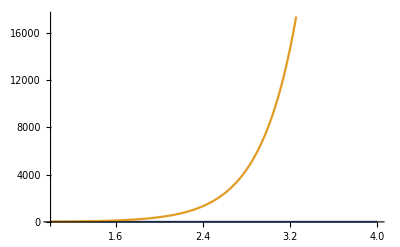

0.30103

0.30103

```mathematica
Plot[{x,g[x]},{x,1,4}]
Log[10,200.]-Log[10,100.]
Log[10,400.]-Log[10,200.]
```

## tmp-2

```mathematica
D[Log[x],{x,1}]
```

1/x

```mathematica
PrimePi[2000000]/PrimePi[1000000]//N
PrimePi[4000000]/PrimePi[2000000]//N
PrimePi[512000000]/PrimePi[256000000]//N
```

1.89728

1.90116

1.92671

```mathematica
PrimePi[256000000]/256000000//N
PrimePi[512000000]/512000000//N
```

0.0546466

0.0526442

```mathematica
1/Log[10^10000]//N
```

0.0000434294